# Improving Quantum Thermal Transistors through Feedback-Controlled Baths

In recent years, the integration of quantum feedback mechanisms into quantum thermal machines has experienced significant growth, driven by the benefits it offers in manipulating the system states. This is particularly advantageous in nano-systems like quantum thermal transistors, which help preserve their inherent quantum properties as they lose the purity of the system states due to decoherence and relaxation from interactions with thermal baths, within the subsystems, and monitoring. Studies have demonstrated that preserving quantum coherence can enhance quantum thermal machine performance, particularly by improving a quantum transistor’s amplification rate, thereby improving its efficiency. In our research, we propose engineering baths to be equipped with detectors and a controller to enable feedback that emulates a role played by a feedback resistor in an electronic transistor. We modify the system evolution trajectories by using a weak monitoring record from one of the detectors. By taking the ensemble average of these trajectories, we unveil the evolution of the system density matrix that corresponds to the Markovian dynamics of the system. This type of feedback via weak monitoring will only introduce minimal perturbation to the system and, once tuned, improve the system coherence that will otherwise diminish due to bath interactions. Furthermore, there will be no change in the relaxation times and the probability of population terms remains the same compared to the original model. We treat this as an improvement in the operational characteristics of the quantum thermal transistor as it preserves its quantum features and enhances its ability to amplify.

In this supplementary material, we provide the code that use to generate all the images.  We acknowledge the use of some modules and functions of  supplementary materials of Refs[13,20,28,36,75]. Note that the reference numbers are from the original manuscript.

```mathematica
ClearAll["Global`*"]
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

## General Model of a Quantum Thermal Transistor (Modeled similar to Ref.11)

First we describe the system description where we consider the terminals of the transistor as two-level systems (TLSs) each having two-states.  We represent the spin states of the two-level systems using the Pauli-matrices described as[Ref.13] :

#### Pauli-Matrices

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
Id[ve_,ho_]:=ve,ho     (*Identity matrix*)
```

The system Hamiltonian is described in Eq.1 is represented using the Mathematica code:

#### System Hamiltonian :

```mathematica
HsSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=
ℏ((ωL/2)Subscript[σ, 3][veL,hoL]Id[veM,hoM]Id[veR,hoR]+
(ωM/2)Id[veL,hoL]Subscript[σ, 3][veM,hoM]Id[veR,hoR]+
(ωR/2)Id[veL,hoL]Id[veM,hoM]Subscript[σ, 3][veR,hoR]+
(ωLM/2)Subscript[σ, 3][veL,hoL]Subscript[σ, 3][veM,hoM]Id[veR,hoR]+
(ωMR/2)Id[veL,hoL]Subscript[σ, 3][veM,hoM]Subscript[σ, 3][veR,hoR]+
(ωRL/2)Subscript[σ, 3][veL,hoL]Id[veM,hoM]Subscript[σ, 3][veR,hoR])

EmapL[i_]:=(i,5+i,6+i,7+i,8)2+(i,1+i,2+i,3+i,4)1
EmapM[i_]:=(i,3+i,4+i,7+i,8)2+(i,1+i,2+i,5+i,6)1
EmapR[i_]:=(i,2+i,4+i,6+i,8)2+(i,1+i,3+i,5+i,7)1
Hs[ve_,ho_]:=HsSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
HsMatrix=Table[Hs[ve,ho],{ve,1,8},{ho,1,8}];
MatrixForm[HsMatrix]
HsEVal[i_]:=(Eigenvalues[HsMatrix][[{8,1,7,2,4,5,3,6}]])[[i]]
HsEVec[i_]:=(Eigenvectors[HsMatrix][[{8,1,7,2,4,5,3,6}]])[[i]]
```

((ωL/2+ωLM/2+ωM/2+ωMR/2+ωR/2+ωRL/2) ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ωL/2+ωLM/2+ωM/2-ωMR/2-ωR/2-ωRL/2) ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ωL/2-ωLM/2-ωM/2-ωMR/2+ωR/2+ωRL/2) ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ωL/2-ωLM/2-ωM/2+ωMR/2-ωR/2-ωRL/2) ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-ωL/2-ωLM/2+ωM/2+ωMR/2+ωR/2-ωRL/2) ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-ωL/2-ωLM/2+ωM/2-ωMR/2-ωR/2+ωRL/2) ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-ωL/2+ωLM/2-ωM/2-ωMR/2+ωR/2-ωRL/2) ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-ωL/2+ωLM/2-ωM/2+ωMR/2-ωR/2+ωRL/2) ℏ)

#### Pauli matrices for the composite system

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=Subscript[σ, P,axis][ve,ho]=
P,1(Subscript[σ, axis][EmapL[ve],EmapL[ho]]Id[EmapM[ve],EmapM[ho]]Id[EmapR[ve],EmapR[ho]])+
P,2(Id[EmapL[ve],EmapL[ho]]Subscript[σ, axis][EmapM[ve],EmapM[ho]]Id[EmapR[ve],EmapR[ho]])+
P,3(Id[EmapL[ve],EmapL[ho]]Id[EmapM[ve],EmapM[ho]]Subscript[σ, axis][EmapR[ve],EmapR[ho]])

Subscript[σmatrix, P_,axis_]:=Subscript[σmatrix, P,axis]=Table[Subscript[σ, P,axis][ve,ho],{ve,1,8},{ho,1,8}]
Subscript[σPmatrix, P_]:=(1/2)(Subscript[σmatrix, P,1]+ⅈ Subscript[σmatrix, P,2])
Subscript[σMmatrix, P_]:=(1/2)(Subscript[σmatrix, P,1]-ⅈ Subscript[σmatrix, P,2])
```

#### Possible Transition Frequencies between the energy levels of the system.

The composite system created created by three two-level systems corresponds to 8 energy levels as we described in Eq.2. Due to these eight energy levels , there will be 28 possible energy jumps (transition frequencies) between the eight energy levels. We wrote this code using the functions described in Ref.20 supplementary material. Note that even though there can be 28 possibilities of transition frequencies, only 12 will be non-zero  as  in Fig. 2 according to our paper.

```mathematica
ωassum={ωL==10,ωM==0.1,ωR==0.0001,ωLM==1.01,ωMR==1,ωRL==0.001,ℏ==1};   (*Assuming values to angular frequencies to generate possible transition frequencies*)
ωassum1=Flatten[{Table[Subscript[ω, {i,j}]->(HsEVal[i]-HsEVal[j] )/ℏ,{i,1,8},{j,1,8}]}];

ω[m_,n_]:=Simplify[(HsEVal[m]-HsEVal[n])/ℏ]

ω[i_]:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]

Table[ω[i],{i,1,ωsize}]
ωsize
```

{-ωMR-ωR-ωRL,-ωLM-ωM-ωMR,-ωLM-ωM+ωR+ωRL,-ωLM-ωM-ωR-ωRL,-ωLM-ωM+ωMR,ωMR-ωR-ωRL,-ωL-ωLM-ωRL,-ωL-ωLM+ωMR+ωR,-ωL+ωM+ωMR-ωRL,-ωL+ωM+ωR,-ωL-ωLM-ωMR-ωR,-ωL-ωLM+ωRL,-ωL+ωM-ωR,-ωL+ωM-ωMR+ωRL,-ωMR-ωR+ωRL,-ωL-ωM-ωMR-ωRL,-ωL-ωM+ωR,-ωL+ωLM-ωRL,-ωL+ωLM-ωMR+ωR,ωLM-ωM-ωMR,ωLM-ωM+ωR-ωRL,-ωL-ωM-ωR,-ωL-ωM+ωMR+ωRL,-ωL+ωLM+ωMR-ωR,-ωL+ωLM+ωRL,ωLM-ωM-ωR+ωRL,ωLM-ωM+ωMR,ωMR-ωR+ωRL}

28

## Describing the Quantum Thermal Transistor Dynamics using the reduced dynamics method

This is the most commonly used method to derive the quantum master equation for the quantum thermal transistor states. The states of the quantum thermal transistor is described by the density matrix. The size of the density matrix is 8*8. In this code snippet,  we initialize the density matrix.

#### Initialization of the density Matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}];
MatrixForm[ρMatrix[t]];
```

To describe the quantum master equation, we need to describe the jump operators as given in Eq.10. As there are 28 possible transitions that can happen, we can describe 28 jump operators arising due to the interaction of a single bath. As there are three baths interacting with the system, the number of jump operators are 3*28. We describe this set of 3*28 jump operators in the ‘temp’ array.  Note that some of the jump operators are zero, indicating that the corresponding jump is not possible.

#### e.g. The (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)in temp [1,7] indicates that there is a jump between energy level 5 and 1 due to bath interaction L and the placement indicates that the energy difference is -ωL-ωLM-ωRL, that can be referred to ω[7]. Hence, the ‘temp’ columns indicates the corresponding bath L,M,R and rows indicates the 28 energy differences.

```mathematica
temp=({{({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}})}});
```

#### Use the following code snippets to generate the Lindblad terms automatically (Ref.11 Supplemental Material for further details)

```mathematica
(*Subscript[A, P_][ve_,ho_,ωs_]:=∑_(i=1)^8 ∑_(j=1)^8 ω[j,i],ωs ve,iho,jSubscript[σ, P,1][j,i];

Subscript[AMatrix, P_][ωs_]:=Subscript[AMatrix, P][ωs]=Simplify[Table[Subscript[A, P][ve,ho,ωs],{ve,1,8},{ho,1,8}],Assumptions->ωassum]
temp=Table[Subscript[AMatrix, P][ω[i]],{P,1,3},{i,1,ωsize}];
MatrixForm[temp]
Subscript[AMatrixω, P_][i_]:=temp[[P,i]]
Table[ω[i],{i,1,ωsize}]*)
```

We used the manually defined temp array to arrange the jump operators. AMatrixω_P_[i_]describe the possible jump operators. Once we describe the jump operators, we define the Lindblad super-operator in Eq.7 using LinMatrix_P[ρ].

```mathematica
Subscript[AMatrixω, P_][i_]:=temp[[P,i]]
ω[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[Subscript[ω, {m,n}],{m,2,8},{n,1,m-1}]];
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Subscript[LinMatrix, P][ρ]=∑_(i=1)^ωsize (J[ω[i]](1+Subscript[NBE, P][ω[i]])(Subscript[AMatrixω, P][i].ρ.Subscript[AMatrixω, P][i]†-(1/2)(Subscript[AMatrixω, P][i]†.Subscript[AMatrixω, P][i].ρ+ρ.Subscript[AMatrixω, P][i]†.Subscript[AMatrixω, P][i]))+J[ω[i]]Subscript[NBE, P][ω[i]](Subscript[AMatrixω, P][i]†.ρ.Subscript[AMatrixω, P][i]-(1/2)(Subscript[AMatrixω, P][i].Subscript[AMatrixω, P][i]†.ρ+ρ.Subscript[AMatrixω, P][i].Subscript[AMatrixω, P][i]†)))
```

#### Master Equation without Monitoring and Feedback

Hence we can represent the differential equation governing the quantum states ρ as in Eq.6 , using the following code.

```mathematica
RHSenv[ρ_]:=Subscript[LinMatrix, 1][ρ]+Subscript[LinMatrix, 2][ρ]+Subscript[LinMatrix, 3][ρ];
RHS=RHSenv[ρMatrix[t]];
LHS=D[ρMatrix[t], t];
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal];
Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,3}]];
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}]];
sol=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol];
```

If working in normalized units,  they are described as follows.

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;  (*Represented as T in the figures and in the paper*)
ωconv=1;  (*Represented as Δ in the figures and in the paper*)
```

For those interested to work in SI units, please use the following conversions. Here, Tconv is defined to be in the range of mK.  We define the maximum as 50 mK (0.5K) to be consistent with the models describe in literature. Refs[20,28,36,74]. The temperature scale can be adjusted appropriately to suit an experimental setup . Here we considered the maximum temperature as 100mK. Meaning that the HOT thermal bath has a temperature of 100mK.

```mathematica
(*unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.5;                (*Represented as T=0.5K in the figures and in the paper for SI units conversion*)
ωconv=(Tconv k)/ℏ/.unitassum;  (*Represented as Δ=0.65 10^11 Hz in the figures and in the paper for SI units conversion*)
Τconv=(Tconv k)/ℏ/.unitassum;*)
```

We assume three distinct temperature values as T_1,T_2,T_3 and the angular frequencies appropriately to be consistent with the previous models of the quantum thermal transistors. We also consider a coupling constant value in here.

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.1 Tconv,Subscript[T, 3]-> 0.02 Tconv,ωL->0ωconv,ωM->0.1 ωconv,ωR->0 ωconv,ωLM->1 ωconv,ωMR->1 ωconv,ωRL->0ωconv,κ->0.01};
```

We treat the baths as a collection of harmonic oscillators, each having a mode with frequency ω, we approximate the populations of these modes to the Planck distribution as in Eq.8 as

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

For an ohmic bath, we represent the spectral density function as in Eq.9 as

```mathematica
Jassum=J[ω_]->κ ω;
```

Next, for time analysis in this manuscript, we describe a maximum time, this is usually considered as the time at which the quantum states achieved a steady state

```mathematica
tmax=(1000000/ωMR)//.Flatten[{unitassum,Tassum}];
```

Next we solve Eq.6  to visualize the the evolution of the system density matrix.

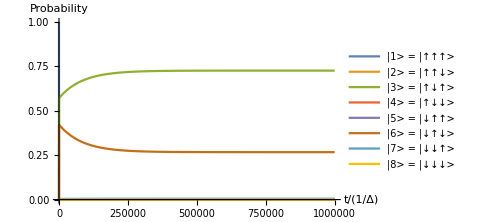

```mathematica
dynamics=NDSolve[
Flatten[{sol//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1}],Table[Subscript[ρ, {i,j}][0]==i,j i,1 1,{i,1,8},{j,1,8}]}]
,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, {i,i}][t],{i,1,8}]}/.dynamics];
plota=Plot[%,{t,0,tmax},PlotRange-> {0.0,1},ImageSize->Medium,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["t/(1/Δ)",FontFamily->"Times New Roman",FontSize->14.5],
Style["Probability",FontFamily->"Times New Roman",FontSize->14.5]}, 
PlotLegends->{
Style["|1> = |↑↑↑> "],
Style["|2> = |↑↑↓> "],
Style["|3> = |↑↓↑> "],
Style["|4> = |↑↓↓> "],
Style["|5> = |↓↑↑> "],
Style["|6> = |↓↑↓> "],
Style["|7> = |↓↓↑> "],
Style["|8> = |↓↓↓> "]}]
```

From this visualization, we clearly see the relaxation rates with the figure indicating the probability of population. This is found in Fig.7. The populations at 6 and 3 are at highest probability as they are the lowest energy states of the system. Please refer to Fig.2 to check for the lowest levels. Note that after 3us (3us=200000 units x (1/Δ)), the transistor attain the steady state. Next we visualize the amplitude of the each state.

```mathematica
temp1a=sol;
temp2a=temp1a//.Flatten[{Jassum,ωassum1,NBEassum,unitassum,Tassum}];
temp3a=Flatten[{temp2a/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4a=Quiet[Flatten[Solve[temp3a,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]]
```

{ρ_{1,1}→3.85451×10^-7,ρ_{1,2}→0.,ρ_{1,3}→0.,ρ_{1,4}→0.,ρ_{1,5}→0.,ρ_{1,6}→0.,ρ_{1,7}→0.,ρ_{1,8}→0.,ρ_{2,1}→0.,ρ_{2,2}→0.00156704,ρ_{2,3}→0.,ρ_{2,4}→0.,ρ_{2,5}→0.,ρ_{2,6}→0.,ρ_{2,7}→0.,ρ_{2,8}→0.,ρ_{3,1}→0.,ρ_{3,2}→0.,ρ_{3,3}→0.726249,ρ_{3,4}→0.,ρ_{3,5}→0.,ρ_{3,6}→0.,ρ_{3,7}→0.,ρ_{3,8}→0.,ρ_{4,1}→0.,ρ_{4,2}→0.,ρ_{4,3}→0.,ρ_{4,4}→0.000233159,ρ_{4,5}→0.,ρ_{4,6}→0.,ρ_{4,7}→0.,ρ_{4,8}→0.,ρ_{5,1}→0.,ρ_{5,2}→0.,ρ_{5,3}→0.,ρ_{5,4}→0.,ρ_{5,5}→0.000233179,ρ_{5,6}→0.,ρ_{5,7}→0.,ρ_{5,8}→0.,ρ_{6,1}→0.,ρ_{6,2}→0.,ρ_{6,3}→0.,ρ_{6,4}→0.,ρ_{6,5}→0.,ρ_{6,6}→0.267056,ρ_{6,7}→0.,ρ_{6,8}→0.,ρ_{7,1}→0.,ρ_{7,2}→0.,ρ_{7,3}→0.,ρ_{7,4}→0.,ρ_{7,5}→0.,ρ_{7,6}→0.,ρ_{7,7}→0.00466104,ρ_{7,8}→0.,ρ_{8,1}→0.,ρ_{8,2}→0.,ρ_{8,3}→0.,ρ_{8,4}→0.,ρ_{8,5}→0.,ρ_{8,6}→0.,ρ_{8,7}→0.,ρ_{8,8}→4.0558×10^-7}

From the observations, It is clear that without monitoring and feedback the coherence terms ρ_{i,j}have become zero. Only population terms ρ_{i,i} in the density matrix are non-zero.

#### Visualizing the energy flows in the transistor, varying with the control temperature T_M.

First let us write a function to find the energy flow . This the energy into the system from bath L, bath M and bath R. Energy flow can be found using Eq.30.

```mathematica
HsMatrixSimp=DiagonalMatrix[ℏ{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6],Subscript[ω, 7],Subscript[ω, 8]}];
```

```mathematica
ωassum2={Table[Subscript[ω, i]-> Hs[i,i]/ℏ,{i,1,8}]};
```

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HsMatrixSimp]
```

```mathematica
varEngyFunc[T1_,T2_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,κ-> 0.01,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[T, 3]-> T3,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];
Re[Flatten[{
Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}],ωassum2,temp0}]/.temp3]]
]
```

```mathematica
Module[{T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs},
T1=0.2Tconv;T2=0.1Tconv;T3=0.02Tconv;
ωLs=0 ωconv;ωMs=0.1 ωconv;ωRs=0 ωconv;ωLMs=1 ωconv;ωMRs=1 ωconv;ωRLs=0ωconv;
varEngyFunc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs]
]
```

{4.70281×10^-6,-3.1521×10^-8,-4.67129×10^-6}

From the results, it is clear that the energy into the system from bath R is negative, meaning that the energy flow is now from system to the bath. This completes the energy flow from bath L to bath R via the system controlled by bath M.  For interested readers, we ask to change T2=0.1Tconv to see if this value is too low than T3, there will not be an energy flow. For a detailed idea on these types of quantum thermal transistors and multi-transistors, please refer to Ref.13 and Ref.36. Next, we use the following function to visualize how the energy flow varies by changing T2. Notice that there is a cut-off phase and with a slight increase with T2, we notice the energy flows now following through the system. The energy flows given in the figure are normalized.  In SI units (with the temperature scale used the value has to be multiplied by .44 10^-18). Ours were tuned to suit the values given in Refs.23,28,36 and 75.

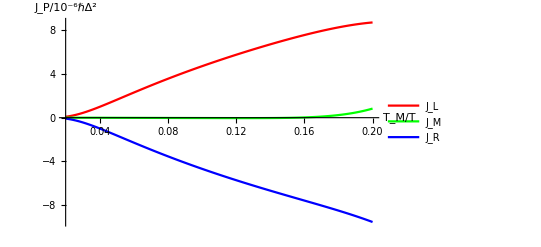

```mathematica
PlotEngyFlowsWithTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp},
tempx=Table[{T2,T2,T2},{T2,T2min,T2max,Tres}];

tempy=10^6 Table[varEngyFunc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,3}];
ListPlot[temp,PlotRange->{{T2min,T2max},Automatic},AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_P/10^-6ℏΔ^2",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{{Red},{Green},{Blue}},PlotLegends->legends &&{
Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_R",FontFamily->"Times New Roman",FontSize->14.5]}]
]

plot1=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.002Tconv;
PlotEngyFlowsWithTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

#### Amplification rate of the quantum thermal transistor defined as : α=∂ J_L/∂ J_M

To understand the transistor action, we visualize the amplification rate using the Eq.35. We visualize both α_L and α_R. Note that α_L=-α_R. When |α_L|,|α_R|>1, we say that the device behaves as a quantum thermal transistors. For interested readers, please refer to Ref.11 for a detailed description on quantum thermal transistors and the transistor action.

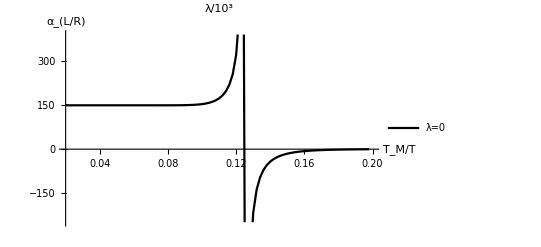

```mathematica
PlotAplificationTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp,tempJH,tempJN,tempampl},

tempy=10^6 Table[varEngyFunc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH=-tempy[[;;,1]];
tempJN=tempy[[;;,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
temp=MapThread[List,{tempx,tempampl}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["α_(L/R)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Black},PlotRange->{{T2min,T2max},Automatic}]


]

plot2=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.002Tconv;
PlotAplificationTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

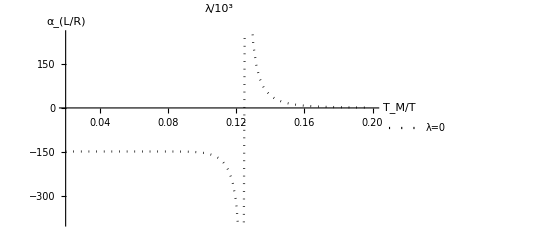

```mathematica
PlotAplificationTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp,tempJH,tempJN,tempampl},

tempy=10^6 Table[varEngyFunc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH=-tempy[[;;,3]];
tempJN=tempy[[;;,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
temp=MapThread[List,{tempx,tempampl}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["α_(L/R)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Black,Dotted},PlotRange->{{T2min,T2max},Automatic}]


]

plot3=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.002Tconv;
PlotAplificationTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

#### Visualization of quantum coherence in the quantum thermal transistor

We write a function to check the quantum coherence in the system. We use Eq. 11 to write this code snippet. Note that this quantum thermal transistor without feedback will give zero quantum coherence at steady state. We also visualize if there is a relationship between the emergence of quantum coherence by changing temperature TM.

```mathematica
Coherencecalc[T1_,T2_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_]:=
Module[{temp0,temp1,temp2,temp3,temp4,temp5,temp6},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,κ-> 0.01,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[T, 3]-> T3,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];


temp1=sol;
temp2=temp1//.temp0;
temp3=Flatten[{temp2/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4=Quiet[Flatten[Solve[temp3,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];
temp5=Delete[temp4,Table[{1+9i},{i,0,7}]];
temp6=Total[Abs[Values[temp5]]]

]


Module[{T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs},
T1=0.2Tconv;T2=0.1Tconv;T3=0.02Tconv;
ωLs=0 ωconv;ωMs=0.1 ωconv;ωRs=0 ωconv;ωLMs=1 ωconv;ωMRs=1 ωconv;ωRLs=0ωconv;
Coherencecalc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs]
]
```

0.

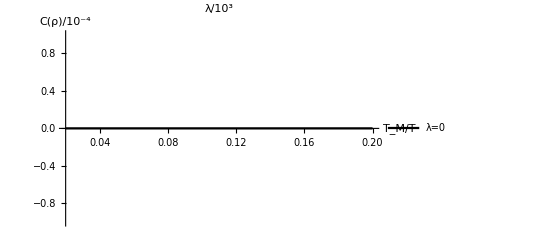

```mathematica
PlotCoherenceTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp},

tempy=10^4 Table[Coherencecalc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max,Tres}];

temp=MapThread[List,{tempx,tempy}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["C(ρ)/10^-4",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{Black},PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0",FontFamily->"Times New Roman",FontSize->14.5]},PlotRange->{{T2min,T2max},Automatic}]


]

plot4=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotCoherenceTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

## Finding the Quantum Thermal Transistor dynamics enabled with monitoring and feedback using the Trajectory Method

Up-to this level, the quantum thermal transistor we describe is already available in the literature. Our code outputs match with the previous studies Refs[13,20,28,36,75] and previous results of relaxation rates, zero quantum coherence, operating temperatures and the amplification rates. In this section we introduce feedback control baths by properly defining feedback control parameters and  measurement strength parameters.

As we introduced, the feedback operator in Eq.26, it consists of a control parameter λ, that determines by how far the states in the x-direction must be flipped. To keep the relaxation rates as same as the original model we described above in the previous sections, we make λ<<κ and λ ⩽ (1/ζ)^(1/2) .

Hence, we use a control parameter λ;

```mathematica
λ=0.0001;
```

Next, we define the measurement strength parameter. The measurement strength parameter was selected such that it will not impair the transistor action. For further details on how to select the measurement parameter, refer to our work in Ref.75.

```mathematica
ζ=0.02;
```

Note, we define feedback Hermitian operator in Eq.26. F= λ(J[ω] (1 +N[ω]))^(1/2)σmatrix_(1,1).  Note that in equation we represented σmatrix_(1,1) as A_M . Here, σmatrix_(1,1) describes all the jumps possible in the system due to the influence of bath-M. This is considering all the possible jumps we describe in temp[2,28], but considered as a single operator removing frequency dependencies. Hence, the operator σmatrix_(1,1) as a whole flips states in x direction similar to how bath-M flips the states in the system independent of frequency.  This can be denoted as σmatrix_(1,1)= AMatrixω_2=∑_(i=1) AMatrixω_1[i]. This can be also found σmatrix_(1,1)=I⊗σmatrix_1⊗I where σmatrix_1 is the Pauli matrix in the x-direction. Refer to the Pauli matrices  for the composite system section to automatically derive this using a code.

```mathematica
Subscript[σmatrix, 1,1]=λ*({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}});
```

Note that we check if this operator satisfies the condition σmatrix_(1,1)=  (σmatrix_(1,1))^+

```mathematica
MatrixForm[Subscript[σmatrix, 1,1]†]
```

(0. | 0. | 0.0001 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0001 | 0. | 0. | 0. | 0.
0.0001 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0001 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0001 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0001
0. | 0. | 0. | 0. | 0.0001 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0001 | 0. | 0.)

```mathematica
MatrixForm[Subscript[σmatrix, 1,1].Subscript[σmatrix, 1,1]†]
```

(1.×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.×10^-8 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.×10^-8 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.×10^-8 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.×10^-8 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.×10^-8 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.×10^-8 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.×10^-8)

Note that in this paper we are not interested in the quantum feedback control for the conditioned states but Markovian dynamics under the feedback. Hence, we consider the new density matrix evolution given by Eq.27. In this equation, additional super-operators appear in addition to the Lindblad superoperator.  Hence, we define the new terms as follows:

We include the following two additional super-operators to describe the master equation

```mathematica
Subscript[FeedMatrix, 1][ρ_]:=-∑_(i=1)^ωsize ⅈ (J[ω[i]])(Subscript[σmatrix, 1,1].Subscript[AMatrixω, 1][i].ρ-Subscript[AMatrixω, 1][i].ρ.Subscript[σmatrix, 1,1]+Subscript[σmatrix, 1,1].ρ.Subscript[AMatrixω, 1][i]†-ρ.Subscript[AMatrixω, 1][i]†.Subscript[σmatrix, 1,1]) ;




Subscript[LinFeedMatrix, 1][ρ_]:=∑_(i=1)^ωsize (J[ω[i]](1+2 Subscript[NBE, 1][ω[i]]))*(1/ζ)(Subscript[σmatrix, 1,1].ρ.Subscript[σmatrix, 1,1]†-(1/2)(Subscript[σmatrix, 1,1]†.Subscript[σmatrix, 1,1].ρ+ρ.Subscript[σmatrix, 1,1]†.Subscript[σmatrix, 1,1]));
```

## Quantum Master Equation with the introduction of monitoring Feedback

With the additional super-operators, we run the new master equation to find the new Markovian dynamics of the system.

### Master Equation after introducing monitoring and feedback

```mathematica
RHSenv1[ρ_]:=Subscript[LinMatrix, 1][ρ]+Subscript[LinMatrix, 2][ρ]+Subscript[LinMatrix, 3][ρ]+Subscript[FeedMatrix, 1][ρ]+Subscript[LinFeedMatrix, 1][ρ];
RHS1=RHSenv1[ρMatrix[t]];

LHS=D[ρMatrix[t], t];
sol1=Flatten[Solve[LHS==RHS1,Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal];
Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,3}]];
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}]];
sol1=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol1];
```

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=1;
```

For working in SI units, temperature is scaled to 50 mK to be consistent with previous studies on quantum thermal transistors.

```mathematica
(*unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.5;
ωconv=(Tconv k)/ℏ/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;*)
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.1 Tconv,Subscript[T, 3]-> 0.02 Tconv,ωL->0ωconv,ωM->0.1ωconv,ωR->0ωconv,ωLM->1ωconv,ωMR->1ωconv,ωRL->0ωconv,κ-> 0.01};
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
Jassum=J[ω_]->κ ω;
```

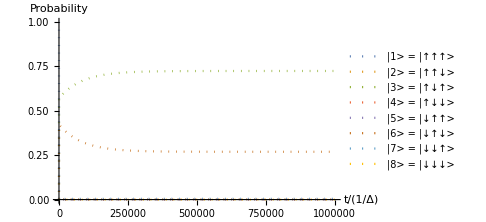

```mathematica
tmax=(1000000/ωMR)//.Flatten[{unitassum,Tassum}];  (*You can vary tmax to study the transient as well as the steady state dynamics*)

dynamics=NDSolve[
Flatten[{sol1//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1}],Table[Subscript[ρ, {i,j}][0]==i,j i,1 1,{i,1,8},{j,1,8}]}]
,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]],{t,0,tmax}
];

Flatten[{Table[Abs[Subscript[ρ, {i,i}][t]],{i,1,8}]}/.dynamics];
plotb=Plot[%,{t,0,tmax},PlotRange-> {0.0,1},ImageSize->Medium,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["t/(1/Δ)",FontFamily->"Times New Roman",FontSize->14.5],
Style["Probability",FontFamily->"Times New Roman",FontSize->14.5]}, 
PlotLegends->{
Style["|1> = |↑↑↑> "],
Style["|2> = |↑↑↓> "],
Style["|3> = |↑↓↑> "],
Style["|4> = |↑↓↓> "],
Style["|5> = |↓↑↑> "],
Style["|6> = |↓↑↓> "],
Style["|7> = |↓↓↑> "],
Style["|8> = |↓↓↓> "]},PlotStyle->Dotted]
```

We have used the parameters such that the relaxation rates are same as the original model even with the introduction of feedback. We notice that with the introduction of monitoring and feedback, the probability of populations will remain the same. This is given in Fig.7 (b). Note that after 3us (3us=200000 units x( 1/Δ)), the transistor attain the steady state. Next we check for the formation of quantum coherence.

### Check formation of coherence terms

```mathematica
temp1a=sol1;
temp2a=temp1a//.Flatten[{Jassum,ωassum1,NBEassum,unitassum,Tassum}];
temp3a=Flatten[{temp2a/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4a=Quiet[Flatten[Solve[temp3a,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]]
```

{ρ_{1,1}→2.82815×10^-6+0. ⅈ,ρ_{1,2}→0,ρ_{1,3}→0,ρ_{1,4}→0,ρ_{1,5}→0,ρ_{1,6}→0,ρ_{1,7}→0.-1.88853×10^-7 ⅈ,ρ_{1,8}→0,ρ_{2,1}→0,ρ_{2,2}→0.00158125+0. ⅈ,ρ_{2,3}→0,ρ_{2,4}→0,ρ_{2,5}→0,ρ_{2,6}→0,ρ_{2,7}→0,ρ_{2,8}→0.-0.000010612 ⅈ,ρ_{3,1}→0,ρ_{3,2}→0,ρ_{3,3}→0.72418+0. ⅈ,ρ_{3,4}→0,ρ_{3,5}→0.+8.33533×10^-7 ⅈ,ρ_{3,6}→0,ρ_{3,7}→0,ρ_{3,8}→0,ρ_{4,1}→0,ρ_{4,2}→0,ρ_{4,3}→0,ρ_{4,4}→0.000236202+0. ⅈ,ρ_{4,5}→0,ρ_{4,6}→0.+0.0000502177 ⅈ,ρ_{4,7}→0,ρ_{4,8}→0,ρ_{5,1}→0,ρ_{5,2}→0,ρ_{5,3}→0.-8.33533×10^-7 ⅈ,ρ_{5,4}→0,ρ_{5,5}→0.000234738+0. ⅈ,ρ_{5,6}→0,ρ_{5,7}→0,ρ_{5,8}→0,ρ_{6,1}→0,ρ_{6,2}→0,ρ_{6,3}→0,ρ_{6,4}→0.-0.0000502177 ⅈ,ρ_{6,5}→0,ρ_{6,6}→0.269115+0. ⅈ,ρ_{6,7}→0,ρ_{6,8}→0,ρ_{7,1}→0.+1.88853×10^-7 ⅈ,ρ_{7,2}→0,ρ_{7,3}→0,ρ_{7,4}→0,ρ_{7,5}→0,ρ_{7,6}→0,ρ_{7,7}→0.00464893+0. ⅈ,ρ_{7,8}→0,ρ_{8,1}→0,ρ_{8,2}→0.+0.000010612 ⅈ,ρ_{8,3}→0,ρ_{8,4}→0,ρ_{8,5}→0,ρ_{8,6}→0,ρ_{8,7}→0,ρ_{8,8}→1.36409×10^-6+0. ⅈ}

Note that unlike in the original model, with the new transistor model with the feedback-controlled baths, some of the coherence terms have now become non-zero. By changing the feedback operators and feedback control parameter we can change the coherence terms and populations in the system. The feedback operator here is tuned such that it provides an enhanced amplification rate for the quantum thermal transistor and feedback output influence is at the input level of the system.

### Visualization of Decoherence rates with time

We visualize the decoherence rate for the feedback-controlled transistor as follows.

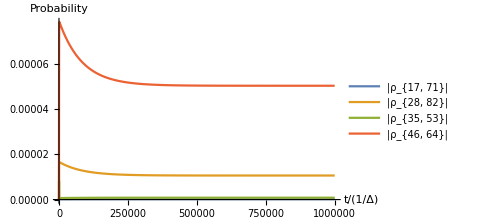

```mathematica
Flatten[{Abs[Subscript[ρ, {1,7}][t]],Abs[Subscript[ρ, {2,8}][t]],Abs[Subscript[ρ, {3,5}][t]],Abs[Subscript[ρ, {4,6}][t]]}/.dynamics];
plotc=Plot[%,{t,0,tmax},PlotRange-> Full, AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["t/(1/Δ)",FontFamily->"Times New Roman",FontSize->14.5],
Style["Probability",FontFamily->"Times New Roman",FontSize->14.5]},ImageSize->Medium,PlotLegends->{"|ρ_{17, 71}|","|ρ_{28, 82}|","|ρ_{35, 53}|","|ρ_{46, 64}|"}]
```

This is given in Fig.6 of the manuscript.

### Visualization of energy flows with time for a quantum thermal transistor under feedback at a steady state

```mathematica
Subscript[EngFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HsMatrix]
Subscript[EngyFlowInfeed1, 1][ρ_]:=Tr[Subscript[FeedMatrix, 1][ρ].HsMatrix]
Subscript[Engyfeed, 1][ρ_]:=Tr[Subscript[LinFeedMatrix, 1][ρ].HsMatrix]
```

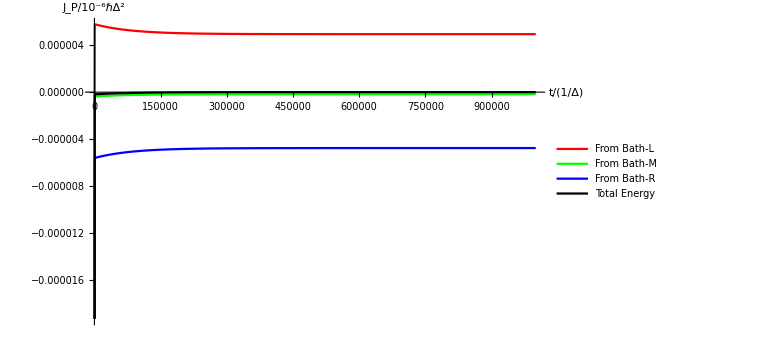

```mathematica
Flatten[{Re[Subscript[EngFlowIn, 1][ρMatrix[t]]]+Re[Subscript[EngyFlowInfeed1, 1][ρMatrix[t]]]+Re[Subscript[Engyfeed, 1][ρMatrix[t]]],Re[Subscript[EngFlowIn, 2][ρMatrix[t]]],Re[Subscript[EngFlowIn, 3][ρMatrix[t]]],Re[Subscript[EngFlowIn, 1][ρMatrix[t]]+Re[Subscript[EngFlowIn, 2][ρMatrix[t]]]+Re[Subscript[EngyFlowInfeed1, 1][ρMatrix[t]]]]+Re[Subscript[Engyfeed, 1][ρMatrix[t]]]+Re[Subscript[EngFlowIn, 3][ρMatrix[t]]]}//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1}]/.dynamics];
Plot[%,{t,0,tmax},AxesStyle->Directive[Darker[Gray],15.5,FontFamily->"Times New Roman"],AxesLabel->{"t/(1/Δ)","J_P/10^-6ℏΔ^2"},ImageSize->Large,PlotLegends->{"From Bath-L","From Bath-M","From Bath-R","Total Energy"},PlotStyle->{Red,Green,Blue,Black}]
```

This image is not in the paper, but we have represented this to show the energy flow rates with the time. From this image is clear the direction of the energy flow is from the system to Bath-R. This shows the energy flow from Bath-L to Bath-R via intermediate bath control through bath M. Note that after 3us (3us=200000 units x (1/Δ)), the transistor attain the steady state.

## Visualizing the energy flows with the temperature under change of trajectory due to feedback

As we did with the original model, now we visualize the energy flows in the system by varying the control bath temperature TM.

```mathematica
Subscript[EngFlowInT, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HsMatrixSimp]
Subscript[EngyFlowInfeed1T, 1][ρ_]:=Tr[Subscript[FeedMatrix, 1][ρ].HsMatrixSimp]
Subscript[EngyfeedT, 1][ρ_]:=Tr[Subscript[LinFeedMatrix, 1][ρ].HsMatrixSimp]
```

```mathematica
varEngyFuncnew1[T1_,T2_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_]:=
Module[{temp0,temp1,temp2,temp3,temp4,temp5,temp6,temp7,temp8,temp9,temp10,temp11},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,κ-> 0.01,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[T, 3]-> T3,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];

temp1=sol1;
temp2=N[temp1//.temp0];
temp3=Flatten[{temp2/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4=temp3;
temp5=Quiet[Flatten[Solve[temp4,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];

temp10=Re[Flatten[{
Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowInfeed1T, 1][ρMatrix[t]]+Subscript[EngyfeedT, 1][ρMatrix[t]],Subscript[EngFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}],ωassum2,temp0}]/.temp5]]


]

Module[{T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs},
T1=0.2Tconv;T2=0.1Tconv;T3=0.02Tconv;
ωLs=0 ωconv;ωMs=0.1 ωconv;ωRs=0 ωconv;ωLMs=1 ωconv;ωMRs=1 ωconv;ωRLs=0ωconv;
varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs]
]
```

{4.92819×10^-6,-1.76869×10^-7,-4.75132×10^-6}

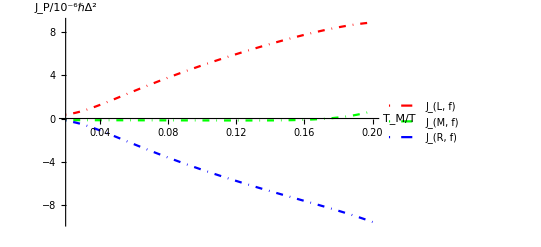

```mathematica
PlotEngyFlowsWithTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp},
tempx=Table[{T2,T2,T2},{T2,T2min,T2max,Tres}];

tempy=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,3}];
ListPlot[temp,PlotRange->{{T2min,T2max},Automatic},AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_P/10^-6ℏΔ^2",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{{Red,DotDashed},{Green,DotDashed},{Blue,DotDashed}},PlotLegends->legends &&{
Style["J_(L, f)",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_(M, f)",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_(R, f)",FontFamily->"Times New Roman",FontSize->14.5]}]
]

plot5=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.002Tconv;
PlotEngyFlowsWithTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

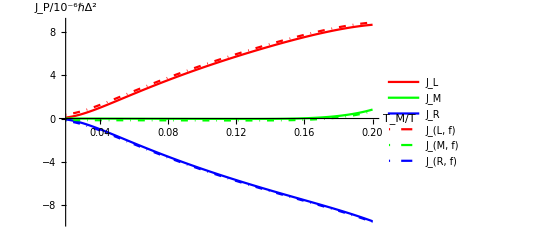

```mathematica
Show[plot1,plot5,PlotRange->All]
```

By plotting the energy flows of the original model and the feedback-control in the same plot, we get the Fig. 5. We notice that with the introduction of tuned feedback, the transistor action  prevails as it follows the energy flow variation similar to that of the original model.

## Visualizing the formation of Coherence with temperature

Next, we visualize the formation of quantum coherence with varying control bath temperature T2.  Note that unlike in the original model , we can clearly see the preservation of quantum coherence as we described in Eq.11, as we get a non-zero value running this code.

```mathematica
Coherencecalc[T1_,T2_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_]:=
Module[{temp0,temp1,temp2,temp3,temp4,temp5,temp6},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,κ-> 0.01,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[T, 3]-> T3,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];


temp1=sol1;
temp2=temp1//.temp0;
temp3=Flatten[{temp2/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4=Quiet[Flatten[Solve[temp3,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];
temp5=Delete[temp4,Table[{1+9i},{i,0,7}]];
temp6=Total[Abs[Values[temp5]]]

]


Module[{T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs},
T1=0.2Tconv;T2=0.1Tconv;T3=0.02Tconv;
ωLs=0 ωconv;ωMs=0.1 ωconv;ωRs=0 ωconv;ωLMs=1 ωconv;ωMRs=1 ωconv;ωRLs=0ωconv;
Coherencecalc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs]
]
```

0.000123704

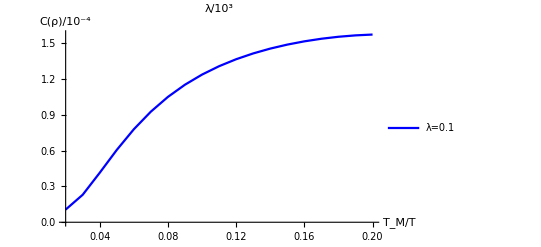

```mathematica
PlotCoherenceTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp},

tempy=10^4 Table[Coherencecalc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max,Tres}];

temp=MapThread[List,{tempx,tempy}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["C(ρ)/10^-4",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{Blue},PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.1",FontFamily->"Times New Roman",FontSize->14.5]},PlotRange->{{T2min,T2max},Automatic}]


]

plot6=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotCoherenceTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

## Visualizing the transistor Amplification rate for different temperatures

#### Amplification rate defined as : α=∂ J_L/∂ J_M

As the amplification rate is the Figure of Merit that describe the transistor action, we visualize how the amplification rate varies with the control temperature. We note that at each temperature variation α>1, showing that the transistor action still prevails.

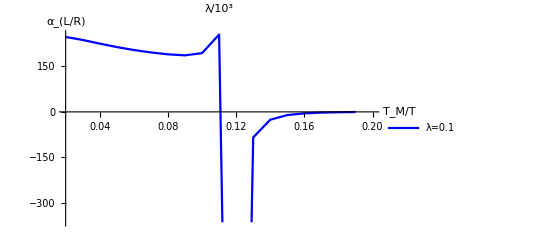

```mathematica
PlotAplificationTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp,tempJH,tempJN,tempampl},

tempy=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH=-tempy[[;;,1]];
tempJN=tempy[[;;,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
temp=MapThread[List,{tempx,tempampl}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["α_(L/R)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.1",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Blue},PlotRange->{{T2min,T2max},Automatic}]


]

plot7=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotAplificationTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

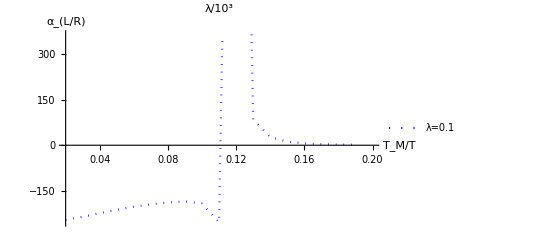

```mathematica
PlotAplificationTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp,tempJH,tempJN,tempampl},

tempy=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH=-tempy[[;;,3]];
tempJN=tempy[[;;,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
temp=MapThread[List,{tempx,tempampl}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["α_(L/R)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.1",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Blue,Dotted},PlotRange->{{T2min,T2max},Automatic}]


]

plot8=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotAplificationTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

We have not put this Figure in the manuscript, but this shows the percentage of improvement of the amplification rate with the original model for the various control temperatures.  This code is useful for the readers to get the straightforward comparison while varying the feedback control parameter λ.

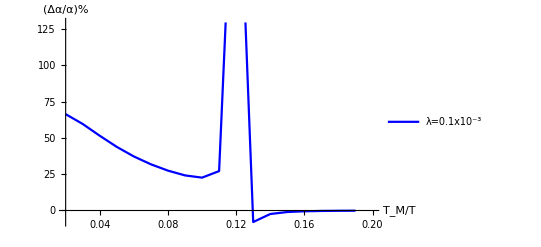

```mathematica
PlotAplificationDifferenceTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy1,tempy2,temp,tempJH1,tempJN1,tempJH2,tempJN2,tempampl,tempamp2,difftemp},

tempy1=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempy2=10^6 Table[varEngyFunc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH1=tempy1[[;;,3]];
tempJN1=tempy1[[;;,2]];
tempJH2=tempy2[[;;,3]];
tempJN2=tempy2[[;;,2]];
tempampl=Differences[tempJH1]/Differences[tempJN1];
tempamp2=Differences[tempJH2]/Differences[tempJN2];
difftemp=(Abs[tempampl-tempamp2]/tempamp2)*100;
temp=MapThread[List,{tempx,difftemp}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["(Δα/α)%",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLegends->{
Style["λ=0.1x10^-3",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Blue},PlotRange->{{T2min,T2max},Automatic}]


]

plot16=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotAplificationDifferenceTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

## Visualizing amplification rate and the quantum coherence for different lambda values by keeping measurement strength parameter fixed

We run the next section to get the  Fig.8 and Fig.9 in the manuscript.

#### For λ=0.00012

```mathematica
λ=0.00012;
```

```mathematica
Subscript[σmatrix, 1,1]=λ*({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}});
```

```mathematica
Subscript[FeedMatrix, 1][ρ_]:=-∑_(i=1)^ωsize ⅈ (J[ω[i]])(Subscript[σmatrix, 1,1].Subscript[AMatrixω, 1][i].ρ-Subscript[AMatrixω, 1][i].ρ.Subscript[σmatrix, 1,1]+Subscript[σmatrix, 1,1].ρ.Subscript[AMatrixω, 1][i]†-ρ.Subscript[AMatrixω, 1][i]†.Subscript[σmatrix, 1,1]) ;




Subscript[LinFeedMatrix, 1][ρ_]:=∑_(i=1)^ωsize (J[ω[i]](1+2 Subscript[NBE, 1][ω[i]]))*(1/ζ)(Subscript[σmatrix, 1,1].ρ.Subscript[σmatrix, 1,1]†-(1/2)(Subscript[σmatrix, 1,1]†.Subscript[σmatrix, 1,1].ρ+ρ.Subscript[σmatrix, 1,1]†.Subscript[σmatrix, 1,1]));



RHSenv1[ρ_]:=Subscript[LinMatrix, 1][ρ]+Subscript[LinMatrix, 2][ρ]+Subscript[LinMatrix, 3][ρ]+Subscript[FeedMatrix, 1][ρ]+Subscript[LinFeedMatrix, 1][ρ];
RHS1=RHSenv1[ρMatrix[t]];

LHS=D[ρMatrix[t], t];
sol1=Flatten[Solve[LHS==RHS1,Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal];
Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,3}]];
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}]];
sol1=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol1];





varEngyFuncnew1[T1_,T2_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_]:=
Module[{temp0,temp1,temp2,temp3,temp4,temp5,temp6,temp7,temp8,temp9,temp10,temp11},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,κ-> 0.01,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[T, 3]-> T3,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];

temp1=sol1;
temp2=N[temp1//.temp0];
temp3=Flatten[{temp2/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4=temp3;
temp5=Quiet[Flatten[Solve[temp4,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];

temp10=Re[Flatten[{
Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowInfeed1T, 1][ρMatrix[t]]+Subscript[EngyfeedT, 1][ρMatrix[t]],Subscript[EngFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}],ωassum2,temp0}]/.temp5]]



]
```

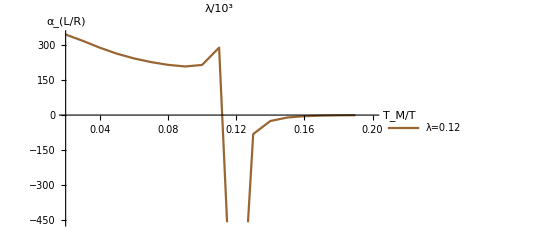

```mathematica
PlotAplificationTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp,tempJH,tempJN,tempampl},

tempy=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH=-tempy[[;;,1]];
tempJN=tempy[[;;,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
temp=MapThread[List,{tempx,tempampl}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style[" α_(L/R)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.12",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Brown},PlotRange->{{T2min,T2max},Automatic}]


]

plot9=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotAplificationTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

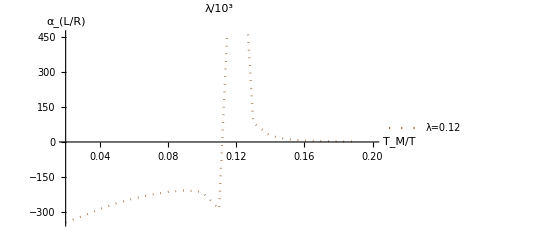

```mathematica
PlotAplificationTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp,tempJH,tempJN,tempampl},

tempy=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH=-tempy[[;;,3]];
tempJN=tempy[[;;,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
temp=MapThread[List,{tempx,tempampl}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style[" α_(L/R)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.12",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Brown,Dotted},PlotRange->{{T2min,T2max},Automatic}]


]

plot10=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotAplificationTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

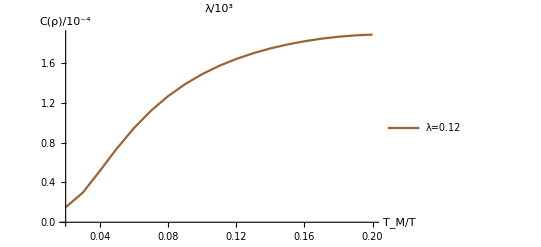

```mathematica
PlotCoherenceTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp},

tempy=10^4 Table[Coherencecalc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max,Tres}];

temp=MapThread[List,{tempx,tempy}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["C(ρ)/10^-4",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{Brown},PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.12",FontFamily->"Times New Roman",FontSize->14.5]},PlotRange->{{T2min,T2max},Automatic}]


]

plot11=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotCoherenceTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

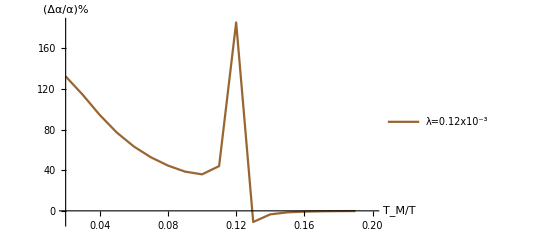

```mathematica
PlotAplificationDifferenceTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy1,tempy2,temp,tempJH1,tempJN1,tempJH2,tempJN2,tempampl,tempamp2,difftemp},

tempy1=10^6 Table[varEngyFuncnew1[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempy2=10^6 Table[varEngyFunc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max-Tres,Tres}];
tempJH1=tempy1[[;;,3]];
tempJN1=tempy1[[;;,2]];
tempJH2=tempy2[[;;,3]];
tempJN2=tempy2[[;;,2]];
tempampl=Differences[tempJH1]/Differences[tempJN1];
tempamp2=Differences[tempJH2]/Differences[tempJN2];
difftemp=(Abs[tempampl-tempamp2]/tempamp2)*100;
temp=MapThread[List,{tempx,difftemp}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["(Δα/α)%",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotLegends->{
Style["λ=0.12x10^-3",FontFamily->"Times New Roman",FontSize->14.5]},PlotStyle->{Brown},PlotRange->{{T2min,T2max},Automatic}]


]

plot17=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotAplificationDifferenceTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

## λ=0.00015

This time we change the control parameter to see the variation of coherence.

```mathematica
λ=0.00015;
```

```mathematica
Subscript[σmatrix, 1,1]=λ*({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}});
```

```mathematica
Subscript[FeedMatrix, 1][ρ_]:=-∑_(i=1)^ωsize ⅈ (J[ω[i]])(Subscript[σmatrix, 1,1].Subscript[AMatrixω, 1][i].ρ-Subscript[AMatrixω, 1][i].ρ.Subscript[σmatrix, 1,1]+Subscript[σmatrix, 1,1].ρ.Subscript[AMatrixω, 1][i]†-ρ.Subscript[AMatrixω, 1][i]†.Subscript[σmatrix, 1,1]) ;




Subscript[LinFeedMatrix, 1][ρ_]:=∑_(i=1)^ωsize (J[ω[i]](1+2 Subscript[NBE, 1][ω[i]]))*(1/ζ)(Subscript[σmatrix, 1,1].ρ.Subscript[σmatrix, 1,1]†-(1/2)(Subscript[σmatrix, 1,1]†.Subscript[σmatrix, 1,1].ρ+ρ.Subscript[σmatrix, 1,1]†.Subscript[σmatrix, 1,1]));



RHSenv1[ρ_]:=Subscript[LinMatrix, 1][ρ]+Subscript[LinMatrix, 2][ρ]+Subscript[LinMatrix, 3][ρ]+Subscript[FeedMatrix, 1][ρ]+Subscript[LinFeedMatrix, 1][ρ];
RHS1=RHSenv1[ρMatrix[t]];

LHS=D[ρMatrix[t], t];
sol1=Flatten[Solve[LHS==RHS1,Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal];
Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,3}]];
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}]];
sol1=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol1];





varEngyFuncnew1[T1_,T2_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_]:=
Module[{temp0,temp1,temp2,temp3,temp4,temp5,temp6,temp7,temp8,temp9,temp10,temp11},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,κ-> 0.01,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[T, 3]-> T3,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];

temp1=sol1;
temp2=N[temp1//.temp0];
temp3=Flatten[{temp2/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp4=temp3;
temp5=Quiet[Flatten[Solve[temp4,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];

temp10=Re[Flatten[{
Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowInfeed1T, 1][ρMatrix[t]]+Subscript[EngyfeedT, 1][ρMatrix[t]],Subscript[EngFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}],ωassum2,temp0}]/.temp5]]



]
```

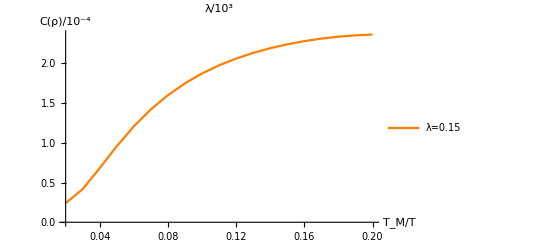

```mathematica
PlotCoherenceTM[T1_,T2min_,T2max_,T3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Tres_,legends_]:=Module[{tempx,tempy,temp},

tempy=10^4 Table[Coherencecalc[T1,T2,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs],{T2,T2min,T2max,Tres}];
tempx=Table[T2,{T2,T2min,T2max,Tres}];

temp=MapThread[List,{tempx,tempy}];
ListPlot[temp,AxesStyle->Directive[Black,13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M/T",FontFamily->"Times New Roman",FontSize->14.5],
Style["C(ρ)/10^-4",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{Orange},PlotLabel->  Style["λ/10^3"],PlotLegends->{
Style["λ=0.15",FontFamily->"Times New Roman",FontSize->14.5]},PlotRange->{{T2min,T2max},Automatic}]


]

plot14=Module[{T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.2Tconv;T3=0.02Tconv;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Tres=0.01Tconv;
PlotCoherenceTM[T1,T2min,T2max,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Tres,True]
]
```

### The variation of amplification rate and the coherence for different λ values.

Now we generate  Fig. 8 and Fig. 9 from the outputs for different λ values.

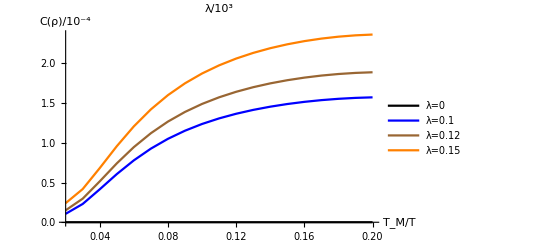

```mathematica
Show[plot4,plot6,plot11,plot14,PlotRange->All]
```

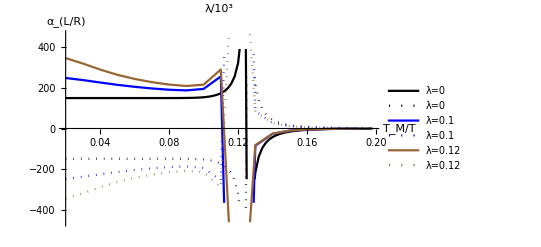

```mathematica
Show[plot2,plot3,plot7,plot8,plot9,plot10,PlotRange->All]
```

For clarity, we represent the list of images that generates from running the above code as follows : Fig.5,Fig.6,Fig.7, Fig.8 and Fig.9.

```mathematica
borderWidth=0;borderColor=RGBColor[0.95,0.95,0.95];
```

```mathematica
border1=Graphics[{Style[Rectangle[{0.02-borderWidth,-10-borderWidth},{0.2+borderWidth,10+borderWidth}],EdgeForm[Thin],FaceForm[None],borderColor]}];
border2=Graphics[{Style[Rectangle[{0-borderWidth,0-borderWidth},{1000000+borderWidth,0.00008+borderWidth}],EdgeForm[Thin],FaceForm[None],borderColor]}];
border3=Graphics[{Style[Rectangle[{0-borderWidth,0-borderWidth},{1000000+borderWidth,1+borderWidth}],EdgeForm[Thin],FaceForm[None],borderColor]}];
border4=Graphics[{Style[Rectangle[{0.02-borderWidth,-500-borderWidth},{0.2+borderWidth,500+borderWidth}],EdgeForm[Thin],FaceForm[None],borderColor]}];
border5=Graphics[{Style[Rectangle[{0.02-borderWidth,0-borderWidth},{0.2+borderWidth,2.5+borderWidth}],EdgeForm[Thin],FaceForm[None],borderColor]}];
```

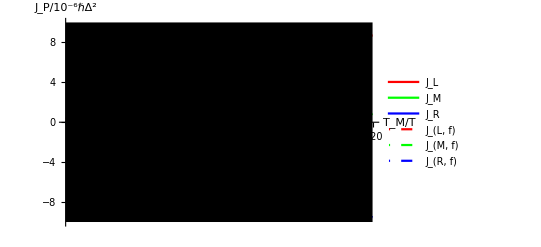

```mathematica
Show[plot1,plot5,border1,PlotRangePadding->None,PlotRange->All]
Show[plotc,border2,PlotRangePadding->None,PlotRange->All]
Show[plota,border3,PlotRangePadding->None,PlotRange->All]
Show[plotb,border3,PlotRangePadding->None,PlotRange->All]
Show[plot2,plot3,plot7,plot8,plot9,plot10,border4,PlotRangePadding->None,PlotRange->All]
Show[plot4,plot6,plot11,plot14,border5,PlotRangePadding->None,PlotRange->All]
```

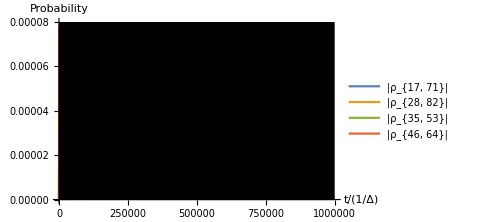

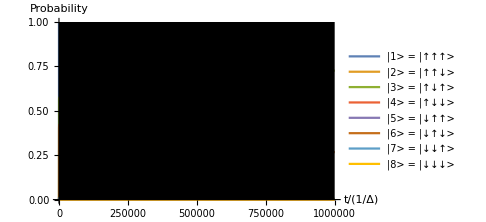

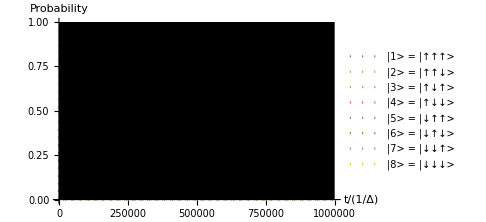

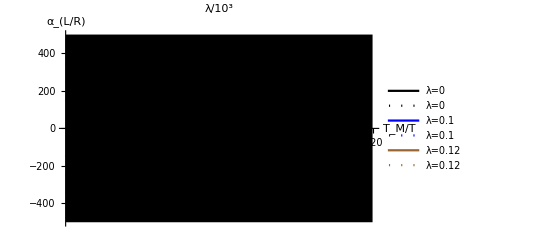

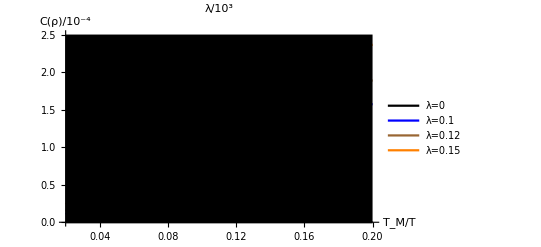

#### For interested readers to understand the heat flow in quantum devices where our code was inspired, refer to the further references we have used.

https://community.wolfram.com/groups/-/m/t/3066097